# Symmetrie und Polstellen für Holo

Nachdem “A korrekt.nb” ein großer Reinfall war und Papier-und-Bleistift Gegenüberstellungen aller Notebooks dazu (also Calc10 und Calc12) ergaben, dass die (n+3)d-Integration offensichtlich richtig ist (Argument: NS2012-FrakturG nachgerechnet, kommt das richtige raus), will ich hier nochmal das Karbstein-Symmtrieargument nachvollziehen, also Geradheit der Funktion f(x) im Integranden f(x)Θ(x)+f(-x)Θ(-x), sowie wie sich die Polstellen dieses Dinges verhalten.

An diesem Dokument wurde nach den numerischen Versuchen weitergearbeitet (4. Mai 2014 und mehr).

An diesem Dokument wurde nach “Symmetrie für Bardeen” weitergearbeitet (7. Mai 2014)

## Symmetrie von ∂_r h(r)

```mathematica
(* Funktionen h'(r) und Integrand der Fouriertrafo *)
hD[z_,n_] = D[1/(1+(1/z)^(2+n)),z];
hDz[z_,n_] = z^(1+n) * hD[z,n];
hDzMinus[z_,n_] = z^(1+n) * hD[-z,n];
```

Tatsächlich wird über z^(1+n) [Thetaspaß]  integriert. Wenn hDz symmetrisch ist, ist der Thetaspaß unnötig. Es ist stets für ungerade n nicht symmetrisch:

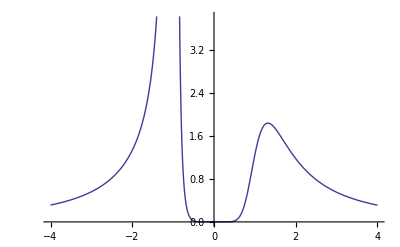

```mathematica
Plot[hDz[z,3],{z,-4,4}]
```

Jetzt recyclen wir nochmal die Polstellenbetrachtung aus Calc10/Polstellen.nb.
Wenn man dort nachschaut, sieht man, dass man durch Kopieren der Polstellen von Re>0 nach Im immer den Fall z=-1  umgehen kann (klar). Anschließend sollte man problemlos die Residuen für Im<0 (da p>0) addieren können.

## Revisiting n=1 aus “A korrekt” (ein Kapitel Unfug)

Wir machen nochmal die Rechnung von n=1, aber diesmal *MIT* Thetafunktionen, wie es korrekt erscheint.

```mathematica
hDzTh[z_,n_] = z^(1+n) * 
(hD[z,n]*HeavisideTheta[z]+ hD[-z,n]*HeavisideTheta[-z])
```

z^(1+n) (((2+n) (-1/z)^(3+n) HeavisideTheta[-z])/((1+(-1/z)^(2+n))^2)+((2+n) (1/z)^(3+n) HeavisideTheta[z])/((1+(1/z)^(2+n))^2))

### A) Integration durch Mathematica: MeijerG

```mathematica
(* Fouriertransformation durch Mathematika,
mit MeijerG als typisches Ergebnis *)
Meijer1=Integrate[hDzTh[z,1]*Exp[-I z p], {z,-∞,∞}]
```

ConditionalExpression[2 √(3/π) MeijerG[{{-1/3},{}},{{0,1/6,1/3,2/3,2/3},{1/2,5/6}},p^6/46656],p∈Reals]

```mathematica
(* Condition war nur interessant fuers Lesen. Wegschmeissen zum Weiterrechnen *)
Meijer1 = Normal[Meijer1];
```

### B) Residuensatz mit der Hand

```mathematica
(* Residuensatz durch die Hand. Wir kennen die eine einzige Wurzel
 mit Im<0 und Re>0 bereits hinreichend aus A korrekt.nb
 (ComplexExpand[] nutzen fuer Re+Im-Darstellung) .
Achtung: Diese Wurzel ist bereits 2-fach entartet. *)
root1 = -(-1)^(2/3);
(* Faktoren:
     2: root1 kommt bei Re>0 und Re<0 vor
 1/p: Wegen dem 2piI/p-Vorfaktor des Integrals
 2: root1 kommt bereits zweimal bei Re>0 vor
2PiI: Residuensatz
-1: Negative Windungszahl
*)
Residue1 =2 /p*2* (2Pi I)(-1)Residue[hDz[z,1]*Exp[-I z p], {z,root1}]
```

(8 (-1)^(5/6) ⅇ^(-(-1)^(1/6) p) (-2+(-1)^(1/6) p) π)/(3 p)

```mathematica
(* Was passiert hier eigentlich, wenn man p~=p*l auf 0 schickt (l->0)?
Mit MeijerG geht der Übergang ja nicht, MeijerG wird dann ∞.  *)
Residue1 /. {p-> 0} // ComplexExpand
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

### B) Numerischer Integration

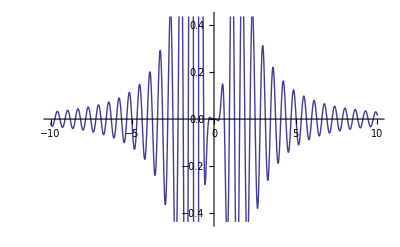

```mathematica
Plot[hDz[z,1]*Exp[-I z 10] // Im,{z,-10,10}]
```

```mathematica
numWert[p_] :=NIntegrate[hDz[z,1]*Exp[-I z p], {z,0,∞},Method-> "MonteCarlo"]
```

```mathematica
numWert[10]
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00091686  + 0.000254324\ ⅈ and 0.00105889 for the integral and error estimates.

0.00091686+0.000254324 ⅈ

TODO HIER: Eine richtige NUMERISCHE Integration machen. Sowas wie in der Zelle hier drüber geht nicht. Das Ergebnis ist dann eine Liste von p-Werten, die womöglich verglichen werden kann mit der kontinuierlichen Integration. Das ganze sollte mit einer einfachen Funktion, die Mathematica integrieren kann (zB x^2 * sin(x) oder so) in einem neuen Worksheet  getestet werden.

### C) Vergleich

```mathematica
(* Plotte diese beiden Ergebnisse *)
```

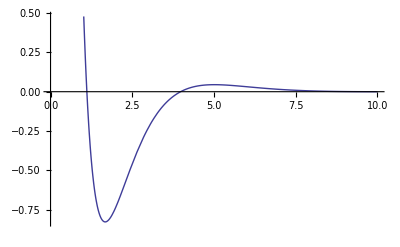

```mathematica
Plot[Residue1 // Re, {p,0,10}]
```

```mathematica
Plot[Normal[Meijer1]//Re,{p,0,10}]
```

$Aborted

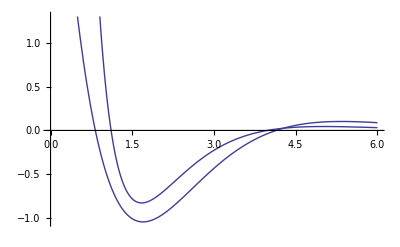

```mathematica
(* Sehen [jetzt nicht mehr] VERDAMMT ähnlich aus! *)
Plot[{Residue1, Normal[Meijer1]}//Re,{p,0,6}]
```

```mathematica
(* Ein numerischer Vergleich *)
compare=({Residue1//Re,Normal[Meijer1]//Re}/. {p-> #} &)/@ Range[0,5,0.3]  // N
```

{{14.5104,1.95441 Re[MeijerG[{{-0.333333},{}},{{0.,0.166667,0.333333,0.666667,0.666667},{0.5,0.833333}},0.]]},{8.1828,2.43436},{3.91614,0.802174},{1.20753,-0.213516},{-0.371969,-0.770286},{-1.16976,-1.0066},{-1.45503,-1.03446},{-1.42786,-0.939035},{-1.2307,-0.781577},{-0.960135,-0.603608},{-0.677786,-0.431259},{-0.419637,-0.279267},{-0.203726,-0.15436},{-0.0361516,-0.0579622},{0.0844002,0.0117466},{0.163381,0.0583295},{0.208122,0.0860593}}

```mathematica
relationships=(#[[2]] / #[[1]] &) /@ compare
```

{0.13469 Re[MeijerG[{{-0.333333},{}},{{0.,0.166667,0.333333,0.666667,0.666667},{0.5,0.833333}},0.]],0.297497,0.204838,-0.17682,2.07083,0.860524,0.710958,0.657653,0.63507,0.62867,0.636276,0.665496,0.757684,1.60331,0.139178,0.357015,0.413503}

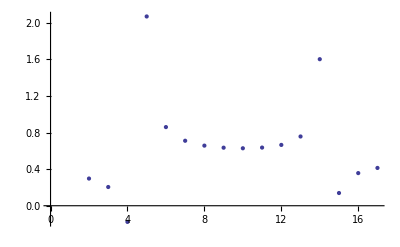

```mathematica
ListPlot[relationships]
```

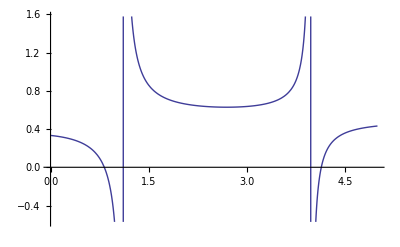

```mathematica
(* Ginge auch einfacher *)
Plot[Re[Normal[Meijer1]] / Re[Residue1], {p,0,5}]
```

Dieser Vergleich der beiden Kurven ist eher Spielerei. Tatsächlich sind sie verschieden und daran kann man nicht viel ändern.
Welche ist richtig? Wie kann man die MeijerG-Funktion verstehen?

## 2. Holographie mit Residuensatz angegangen, für allgemeine n

Den Ansatz, die Polstellen an der y-Achse einfach zu spiegeln, kann man auch für allgemeine n fortsetzen. Das Ergebnis dürfte eine Tabelle sein, die dem Endergebnis von Calc10 entspricht, also ein A für beliebige n findet.

In “A korrekt.nb” hab ich sowas eigentlich schonmal geschrieben. War davon halt damals nicht besonders überzeugt.

Gehalten an den Formalismus von Calc10(Polstellen.nb) und (A korrekt.nb)

```mathematica
ClearAll[polstellen];
polstellen[n_]:=Solve[Denominator[hDz[z,n]] == 0,z] /. {{z-> b_}-> b}
polstellenNeg[n_] := Solve[Denominator[hDzMinus[z,n]] == 0,z] /. {{z-> b_}-> b}
(* nur die Pole, die uns interessieren *)
unserePolstellen[n_] := Select[polstellen[n], Im[#]≤ 0∧Re[#]≥ 0&]
```

Zur “Absicherung” nach der Entdeckung, dass für Re<0 eigentlich die korrekt errechneten Polstellen von hDzMinus genommen werden müssen, plotte ich ein bisschen weiter unten die polstellenNeg zusammen mit den polstellen. Man sieht dort, dass bei Holo h(r) es keinen Unterschied macht, ob man die polstellen spiegelt oder die polstellenNeg nimmt.

```mathematica
(* "richtig" an der Y-Achse spielen, wie es das Betrags/Θ-Zeug erfordert *)
ReConjugate[z_] = -Re[z]+I *Im[z];
(* Vorsicht bei Polen mit Re[z]==0! Die sollen nicht gedoppelt werden. *)
(* Dopplung aller Pole inkl. so, dass man weiß, wo die Dopplung her kommt. Dann: Flatten. *)
allUnserePolstellen[n_] := {#,If[Re[#]>0,{ReConjugate[#]},{}]}&/@ unserePolstellen[n] // Flatten
```

```mathematica
(* Tally kann die Vielfachheiten der Polstellen extrahieren.
zB: Tally[{a,a,b,c}]={{a,2},{b,1},{c,1}}.
Nutze ich aber doch nicht. *)
ResidueList[n_] :=
Join[
 ((2Pi I) (-1) If[Re[#]<0,
(* Residue kann mit Abs/Θ/If nicht umgehen, daher muss die
Fallunterscheidung ausserhalb des "Residues" erfolgen
(daher klappt hDzAbs[z,n] auch nicht) *)
Residue[hDzMinus[z,n]*Exp[-I p z],{z,#}],
Residue[hDz[z,n]*Exp[-I p z],{z,#}]] &)/@ allUnserePolstellen[n]
]
```

### 2.1. Zeichnung der Holographie-Polstellen

Zunächst zum “Manipulieren” und Testen eine interaktive Version.

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
circle[s_Circle]:=s/.Circle[a_,r_,{start_,end_}]:>({s,Arrow[{#-r/10^2 {-Sin@end,Cos@end},#}]}&[a+r {Cos@end,Sin@end}])
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellen[n],
{Re[#], Im[#]} & /@ polstellenNeg[n],
{Re[#], Im[#]} & /@ allUnserePolstellen[n] (* in Ringen *)
}
MakePlot[n_,
label_:"z*h(z) left and right roots vs unit roots. black: Residual taken Points"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Blue, Opacity[0.6],Disk[]}], 0.1},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@circle[Circle[{0,0},1,{0.1,Pi/(2+n) - 0.1 (* 0.1=our cirlce radius *)}]]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,7,1}]
```

Nun zwecks Export den ganzen Spaß nochmal, abgeschrieben aus “Symmetire für Bardeen”.

```mathematica
image=GraphicsGrid[
ArrayReshape[Join[
{ Rasterize[Show@
With[{fun = hDz[#,0]&},ParametricPlot[
(*just need a vis function that will allow x and y to be in the color function*)
{x,y},{x,-1.2,1.2},{y,-1.2,1.2},
(*color and mesh functions don't trigger refinement,so just use a big grid*)
PlotPoints->50,MaxRecursion->0,Mesh->50,(*turn off scaling so we can do computations with the actual complex values*)
ColorFunctionScaling->False,ColorFunction->(Hue[
(*hue according to argument,with shift so arg(z)==0 is red*)
Rescale[Arg[fun[#+I #2]],{-π,π},{0,1}+0.5],1,
(*fudge brightness a bit:
0.1 keeps things from getting too dark,
2 forces some actual bright areas*)
Rescale[Abs[fun[#+I #2]],{0,1.6},{0.21,1}]]&),
(*mesh lines according to magnitude,scaled to avoid the pole at z=1*)MeshFunctions->{Log[Abs[fun[#1+I #2]]]&},
Frame-> True,
ImageSize-> Medium,
PlotRange-> All,
FrameTicksStyle-> (FontOpacity-> 0.5),
BaseStyle->{FontSize->10} (* for export *)
]
],
 "Image", ImageResolution-> 300]
},
Table[Show[
ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
PlotMarkers -> {
{Graphics[{Blue, Opacity[0.6],Disk[]}], 0.1},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12}
},
PlotRange-> All,
FrameTicksStyle-> (FontOpacity-> 0.5),
ImageSize-> Medium
],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{130,130},{0,0}]]
],{n,0,7}]
], {3,3}]
]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../plots/holo-poles.pdf", Show@image]
```

../plots/holo-poles.pdf

Das hier exportierte Bild wurde in calc12.pdf aufgenommen.

### 2.2. Berechnung des Holographie-Integrals

```mathematica
(* Nicht vergessen: 1/p aus Formel 14 Calc10 wg Karbstein-Formel *)
IntegralWert[n_] := 1/p * ( ResidueList[n]//Total ) // Expand
```

```mathematica
IntegralWert[0]
```

-2 ⅇ^-p π+(2 ⅇ^-p π)/p

```mathematica
(N[IntegralWert[0]/.{p->1.515} ] // Re)
```

-0.469481

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# myPoles","Wert für Cell["A(p)"]", "Re?", "Im?"}},
Table[{n,
First[Dimensions[allUnserePolstellen[n]]],
IntegralWert[n] // ComplexExpand ,
(* For a quick check if real/complex part vanishes, evaluate on an arbitrary
   p and check for the value *)
If[(IntegralWert[n]/.{p-> 1.515} //N //Re//Abs)> 10^(-5), Item[✓,Background-> Green],],
If[(IntegralWert[n]/.{p-> 1.515} //N //Im//Abs)> 10 ^(-5), Item[✓, Background->Red],]
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # myPoles | Wert für Cell["A(p)"] | Re? | Im?
0 | 2 | -2 ⅇ^-p π+(2 ⅇ^-p π)/p | ✓ | 
1 | 4 | -8/3 ⅇ^(-(√3 p)/2) π Cos[p/2]+(8 ⅇ^(-(√3 p)/2) π Cos[p/2])/(√3 p)-(8 ⅇ^(-(√3 p)/2) π Sin[p/2])/(3 p) | ✓ | 
2 | 4 | ⅈ (-(3 √2 ⅇ^(-p/(√2)) π Cos[p/(√2)])/p+2 ⅇ^(-p/(√2)) π Sin[p/(√2)]-(3 √2 ⅇ^(-p/(√2)) π Sin[p/(√2)])/p) |  | ✓
3 | 4 | -4/5 ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p]+(16 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(5 p)-(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Cos[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3)+(16384 √(2 (5-√5)) ⅇ^(-1/2 √(1/2 (5-√5)) p) π Cos[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3 p)+(4 ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(5 p)+(4 ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(√5 p)-(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Sin[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3 p)-(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Sin[p/4+(√5 p)/4])/(√5 (2 (5-√5)+(1+√5)^2)^3 p)+ⅈ (-(4 ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(5 p)-(4 ⅇ^(-√(5/8-(√5)/8) p) π Cos[1/4 (-1-√5) p])/(√5 p)+(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Cos[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3 p)+(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Cos[p/4+(√5 p)/4])/(√5 (2 (5-√5)+(1+√5)^2)^3 p)-4/5 ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p]+(16 √(5/8-(√5)/8) ⅇ^(-√(5/8-(√5)/8) p) π Sin[1/4 (-1-√5) p])/(5 p)-(16384 ⅇ^(-1/2 √(1/2 (5-√5)) p) π Sin[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3)+(16384 √(2 (5-√5)) ⅇ^(-1/2 √(1/2 (5-√5)) p) π Sin[p/4+(√5 p)/4])/(5 (2 (5-√5)+(1+√5)^2)^3 p)) | ✓ | 
4 | 6 | -2/3 ⅇ^-p π+(10 ⅇ^-p π)/(3 p)+ⅈ (-(10 ⅇ^(-p/2) π Cos[(√3 p)/2])/(√3 p)+4/3 ⅇ^(-p/2) π Sin[(√3 p)/2]-(10 ⅇ^(-p/2) π Sin[(√3 p)/2])/(3 p)) | ✓ | ✓
5 | 8 | -4/7 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]]-4/7 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]]+(24 ⅇ^(-p Cos[π/14]) π Cos[π/14] Cos[p Sin[π/14]])/(7 p)+(24 ⅇ^(-p Cos[π/14]) π Cos[π/14] Cos[p Sin[π/14]])/(7 p (Cos[π/14]^2+Sin[π/14]^2))-(4 ⅇ^(-p Cos[π/14]) π Cos[π/14]^2 Cos[p Sin[π/14]])/(7 (Cos[π/14]^2+Sin[π/14]^2))-(4 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]] Sin[π/14]^2)/(7 (Cos[π/14]^2+Sin[π/14]^2))+(24 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]] Sin[π/7])/(7 p)-(4 ⅇ^(-p Sin[π/7]) π Cos[π/7]^2 Cos[p Cos[π/7]])/(7 (Cos[π/7]^2+Sin[π/7]^2))+(24 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]] Sin[π/7])/(7 p (Cos[π/7]^2+Sin[π/7]^2))-(4 ⅇ^(-p Sin[π/7]) π Cos[p Cos[π/7]] Sin[π/7]^2)/(7 (Cos[π/7]^2+Sin[π/7]^2))-(24 ⅇ^(-p Sin[π/7]) π Cos[π/7] Sin[p Cos[π/7]])/(7 p)-(24 ⅇ^(-p Sin[π/7]) π Cos[π/7] Sin[p Cos[π/7]])/(7 p (Cos[π/7]^2+Sin[π/7]^2))-(24 ⅇ^(-p Cos[π/14]) π Sin[π/14] Sin[p Sin[π/14]])/(7 p)-(24 ⅇ^(-p Cos[π/14]) π Sin[π/14] Sin[p Sin[π/14]])/(7 p (Cos[π/14]^2+Sin[π/14]^2))+ⅈ (-(24 ⅇ^(-p Sin[π/7]) π Cos[π/7] Cos[p Cos[π/7]])/(7 p)-(24 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]] Sin[π/14])/(7 p)+(24 ⅇ^(-p Cos[π/14]) π Cos[p Sin[π/14]] Sin[π/14])/(7 p (Cos[π/14]^2+Sin[π/14]^2))+(24 ⅇ^(-p Sin[π/7]) π Cos[π/7] Cos[p Cos[π/7]])/(7 p (Cos[π/7]^2+Sin[π/7]^2))+4/7 ⅇ^(-p Sin[π/7]) π Sin[p Cos[π/7]]-(24 ⅇ^(-p Sin[π/7]) π Sin[π/7] Sin[p Cos[π/7]])/(7 p)-(4 ⅇ^(-p Sin[π/7]) π Cos[π/7]^2 Sin[p Cos[π/7]])/(7 (Cos[π/7]^2+Sin[π/7]^2))+(24 ⅇ^(-p Sin[π/7]) π Sin[π/7] Sin[p Cos[π/7]])/(7 p (Cos[π/7]^2+Sin[π/7]^2))-(4 ⅇ^(-p Sin[π/7]) π Sin[π/7]^2 Sin[p Cos[π/7]])/(7 (Cos[π/7]^2+Sin[π/7]^2))+4/7 ⅇ^(-p Cos[π/14]) π Sin[p Sin[π/14]]-(24 ⅇ^(-p Cos[π/14]) π Cos[π/14] Sin[p Sin[π/14]])/(7 p)+(24 ⅇ^(-p Cos[π/14]) π Cos[π/14] Sin[p Sin[π/14]])/(7 p (Cos[π/14]^2+Sin[π/14]^2))-(4 ⅇ^(-p Cos[π/14]) π Cos[π/14]^2 Sin[p Sin[π/14]])/(7 (Cos[π/14]^2+Sin[π/14]^2))-(4 ⅇ^(-p Cos[π/14]) π Sin[π/14]^2 Sin[p Sin[π/14]])/(7 (Cos[π/14]^2+Sin[π/14]^2))) | ✓ | 
6 | 8 | -1/2 ⅇ^(-p Sin[π/8]) π Cos[p Cos[π/8]]+1/2 ⅇ^(-p Sin[π/8]) π Cos[π/8]^2 Cos[p Cos[π/8]]-1/2 ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]]+1/2 ⅇ^(-p Cos[π/8]) π Cos[π/8]^2 Cos[p Sin[π/8]]+1/2 ⅇ^(-p Sin[π/8]) π Cos[p Cos[π/8]] Sin[π/8]^2+1/2 ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]] Sin[π/8]^2+ⅈ (-(7 ⅇ^(-p Sin[π/8]) π Cos[π/8] Cos[p Cos[π/8]])/p-(7 ⅇ^(-p Cos[π/8]) π Cos[p Sin[π/8]] Sin[π/8])/p+1/2 ⅇ^(-p Sin[π/8]) π Sin[p Cos[π/8]]+1/2 ⅇ^(-p Sin[π/8]) π Cos[π/8]^2 Sin[p Cos[π/8]]-(7 ⅇ^(-p Sin[π/8]) π Sin[π/8] Sin[p Cos[π/8]])/p+1/2 ⅇ^(-p Sin[π/8]) π Sin[π/8]^2 Sin[p Cos[π/8]]+1/2 ⅇ^(-p Cos[π/8]) π Sin[p Sin[π/8]]-(7 ⅇ^(-p Cos[π/8]) π Cos[π/8] Sin[p Sin[π/8]])/p+1/2 ⅇ^(-p Cos[π/8]) π Cos[π/8]^2 Sin[p Sin[π/8]]+1/2 ⅇ^(-p Cos[π/8]) π Sin[π/8]^2 Sin[p Sin[π/8]]) |  | ✓
7 | 8 | -8/9 ⅇ^(-(√3 p)/2) π Cos[p/2]+(32 ⅇ^(-(√3 p)/2) π Cos[p/2])/(3 √3 p)-4/9 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]]-(32 ⅇ^(-(√3 p)/2) π Sin[p/2])/(9 p)+(32 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]] Sin[π/9])/(9 p)-(4 ⅇ^(-p Sin[π/9]) π Cos[π/9]^2 Cos[p Cos[π/9]])/(9 (Cos[π/9]^2+Sin[π/9]^2))+(32 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]] Sin[π/9])/(9 p (Cos[π/9]^2+Sin[π/9]^2))-(4 ⅇ^(-p Sin[π/9]) π Cos[p Cos[π/9]] Sin[π/9]^2)/(9 (Cos[π/9]^2+Sin[π/9]^2))-(32 ⅇ^(-p Sin[π/9]) π Cos[π/9] Sin[p Cos[π/9]])/(9 p)-(32 ⅇ^(-p Sin[π/9]) π Cos[π/9] Sin[p Cos[π/9]])/(9 p (Cos[π/9]^2+Sin[π/9]^2))+ⅈ (-(32 ⅇ^(-p Sin[π/9]) π Cos[π/9] Cos[p Cos[π/9]])/(9 p)+(32 ⅇ^(-p Sin[π/9]) π Cos[π/9] Cos[p Cos[π/9]])/(9 p (Cos[π/9]^2+Sin[π/9]^2))+4/9 ⅇ^(-p Sin[π/9]) π Sin[p Cos[π/9]]-(32 ⅇ^(-p Sin[π/9]) π Sin[π/9] Sin[p Cos[π/9]])/(9 p)-(4 ⅇ^(-p Sin[π/9]) π Cos[π/9]^2 Sin[p Cos[π/9]])/(9 (Cos[π/9]^2+Sin[π/9]^2))+(32 ⅇ^(-p Sin[π/9]) π Sin[π/9] Sin[p Cos[π/9]])/(9 p (Cos[π/9]^2+Sin[π/9]^2))-(4 ⅇ^(-p Sin[π/9]) π Sin[π/9]^2 Sin[p Cos[π/9]])/(9 (Cos[π/9]^2+Sin[π/9]^2))) | ✓ |

### 2.3. Untersuchung der Ergebnisse des Holographie-Integrals: Manipulate und Tabelle

Diese Werte sind bislang meiner Weisheit letzter Schluss (26.04.14).
Daran (an der Weisheit) hat sich mittlerweile nicht mehr viel geändert (08.05.14).

Ein Schieber, um  sich zu allen A mal den Real- und Imaginärteil anzuschauen:

```mathematica
Manipulate[
{Plot[Re[#],{p,0,10},ImageSize-> Medium],Plot[Im[#],{p,0,10},ImageSize-> Medium]}& /@ {IntegralWert[n]},
{n,0,7,1}]
```

Plots der Real- und Imaginärteile aller A.
Dazu untersuche ich etwas detaillierter als oben, ob Real/Imaginaerteil wegfaellt, naemlich mit Summierung über ziemlich viele (ca 100) Punkte, statt wie oben nur einen anzuschauen. Witzigerweise ist das Ergebnis aber das gleiche.

```mathematica
(* Real- und Imaginaerteil der Ausintegration (physikalisch Funktion "A^(-2)[p]") *)
{reValues,imValues} = Table[#@IntegralWert[n]//ComplexExpand,{n,0,7}]& /@{Re,Im};
```

```mathematica
(* Index-Positionen, bei welchen n die Real/Imaginaer-Teile nicht wegfallen,
per Summierung der Wertetabelle ("diskrete Integration") ermittelt *)
{reIndex,imIndex} = Function[ary,
((#-> Abs@Total@Table[ary[[#]],{p,0.5,10,0.1}]&/@ Range@Length@ary )
~Select~( (* Rule[a,b]*)#[[2]] > 0.3&))~Cases~ (Rule[n_,_]-> n)
] /@ {reValues, imValues}
```

{{1,2,4,5,6,8},{3,5,7}}

```mathematica
Grid[{
{Style["n",{Blue, Bold, 12}]}~Join~Range[0,7],
{Style["Re",{Blue, Bold, 12}]}~Join~Table[If[MemberQ[reIndex,n+1],Item[✓,Background-> Green],],{n,0,7}],
{Style["Im",{Blue, Bold, 12}]}~Join~Table[If[MemberQ[imIndex,n+1],Item[✓,Background-> Red],],{n,0,7}]
}, Frame-> All]
```

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
Re | ✓ | ✓ |  | ✓ | ✓ | ✓ |  | ✓
Im |  |  | ✓ |  | ✓ |  | ✓ |

### 2.4. Erste Exports von Real- und Imaginaerplots

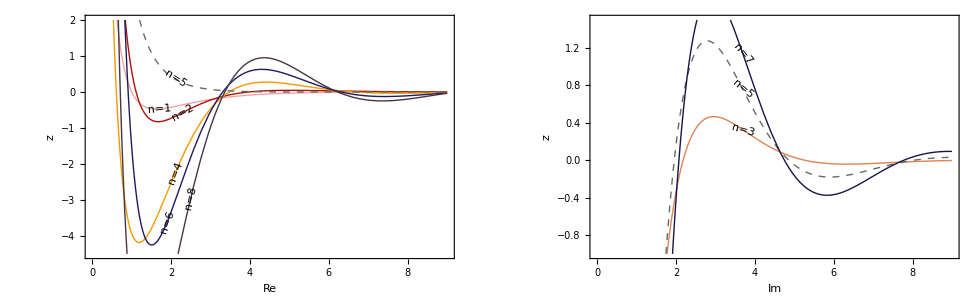

```mathematica
imgsize = 280;
(* Diese Epilabels ist von Calc11 kopiert und abgewandelt, um eine Liste von xpoints
zu akzeptieren, eine Auswertungs/Ableitungsvariable deriv und vor allem eine Liste von
Funktionen (eigentlich nur Ausdrücke) statt einer Funktion von Listen auszuwerten. *)
EpiLabels[xpoint_,data_, labels_,deriv_:r]:= 
Text[
Rotate[labels[[#]],ArcTan[D[ data[[#]],deriv]/.{deriv-> xpoint[[#]]}]],
{xpoint[[#]], 0 + data[[#]]/.deriv-> xpoint[[#]]},
Background -> White
(* Opacity[0.8,White]*)
] & /@ Range@Length@data 
colors = ColorData[9,"ColorList"];
colors[[5]] = {Dashed,colors[[5]]}; (* n=5 has both Re and Im parts, make visible *)
plot2=GraphicsGrid[ {{
Plot[
Evaluate@reValues[[reIndex]],{p,0,9},PlotRange-> {-4.5,2},
ImageSize-> {Automatic, imgsize},
FrameLabel -> {"Re","z"},
Frame->True,
PlotStyle->colors[[reIndex]],
Epilog->EpiLabels[{1.7,2.3,2.1,2.1,1.9,2.5},Evaluate@reValues[[reIndex]], "n="<>ToString[#]&/@reIndex,p]
],Plot[
Evaluate@imValues[[imIndex]],{p,0,9}, PlotRange-> {-1,1.5}, 
Frame->True,
ImageSize-> {Automatic, imgsize},
FrameLabel-> {"Im","z"},
PlotStyle-> colors[[imIndex]],
Epilog->EpiLabels[{3.7,3.7,3.7},Evaluate@imValues[[imIndex]], "n="<>ToString[#]&/@imIndex,p]
]
}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../plots/holo-A.pdf", Show@plot2]
```

../plots/holo-A.pdf

### 2.5. Korrekte Dimensionierung (Skalierung) mit r_0 in n dim

Mein Integralwert ist bislang noch nicht mit den Vorfaktoren (vor allem i) malgenomen worden, außerdem noch nicht mit ^(-1/2) potenziert worden. Eine korrekte Sklaierung der Achsen mittels L ist auch noch nicht erfolgt.
Hier der Radius r_0 für Holographie in n Dimensionen (Calc11):

```mathematica
r0[n_]=(1/(1+n))^(1/(2+n));
Table[r0[n],{n,0,7}]//N
```

{1.,0.793701,0.759836,0.757858,0.764724,0.774169,0.784084,0.793701}

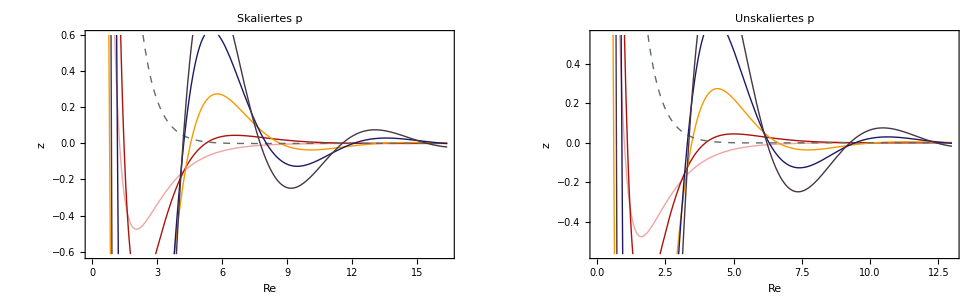

```mathematica
scaledRe = Table[reValues[[n]]/.{p-> p * r0[n]},{n,reIndex}];
GraphicsGrid[ {{ Plot[
Evaluate@scaledRe,{p,0,13/0.7937},
ImageSize-> {Automatic, imgsize},
FrameLabel -> {"Re","z"},
Frame->True,
PlotStyle->colors[[reIndex]],
PlotLabel-> "Skaliertes p"
],  Plot[
Evaluate@reValues[[reIndex]],{p,0,13},
ImageSize-> {Automatic, imgsize},
FrameLabel -> {"Re","z"},
Frame->True,
PlotStyle->colors[[reIndex]],
PlotLabel-> "Unskaliertes p"
]}}]
```

Also ich denke: Man sieht, dass man nichts sieht. Hier lohnt es sich wohl nicht weiter, zu investigieren.

### 2.6. Umstellen nach A

Jetzt nehmen wir mal das Integral hübsch mit seinen Vorfaktoren mal. Also vor allem eigentlich der imaginaeren Einheit.

```mathematica
A[integral_] = (I/p * integral) (*^(-1/2);*)
{reA,imA} = Table[#@ A@IntegralWert[n],{n,0,7}]& /@{Re,Im};
```

(ⅈ integral)/p

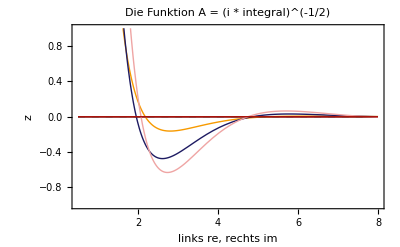
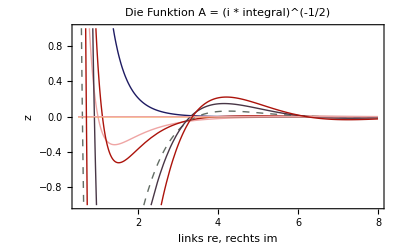

```mathematica
Plot[
Evaluate@#,{p,0.5,8},
ImageSize-> {Automatic, imgsize},
PlotRange-> {-1,1},
FrameLabel -> {"links re, rechts im","z"},
Frame->True,
PlotStyle->colors[[reIndex]],
PlotLabel-> "Die Funktion A = (i * integral)^(-1/2)"
]&/@ {reA,imA}
```

Hier kann man leider kaum was erkennen. Außer, dass A hübsch bei p=0 abfällt. Weiß gerade nicht, ob das irgendwie wünschenswert ist oder so.

Betrachten wir das ganze doch mal für n=1 (da ja bei n=0 bloß 0 rauskommt).

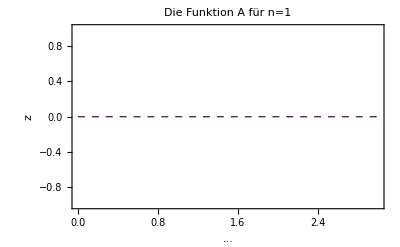
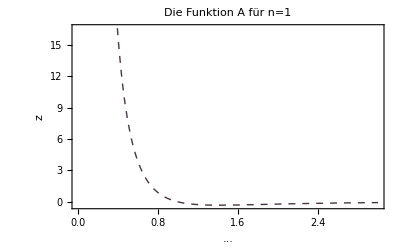

```mathematica
Plot[
Evaluate@#[[1]],{p,0,3},
ImageSize-> {Automatic, imgsize},
FrameLabel -> {"...","z"},
Frame->True,
PlotStyle->colors[[reIndex]],
PlotLabel-> "Die Funktion A für n=1"
]&/@ {reA,imA}
```

```mathematica
IntegralWert[0] // ComplexExpand
A@IntegralWert[0] 
A@IntegralWert[0]  // ComplexExpand
```

-2 ⅇ^-p π+(2 ⅇ^-p π)/p

(ⅈ (-2 ⅇ^-p π+(2 ⅇ^-p π)/p))/p

ⅈ ((2 ⅇ^-p π)/p^2-(2 ⅇ^-p π)/p)

```mathematica
ⅈ ((2 ⅇ^-p π)/p^2-(2 ⅇ^-p π)/p)/.{p-> L p}
```

ⅈ ((2 ⅇ^(-L p) π)/(L^2 p^2)-(2 ⅇ^(-L p) π)/(L p))

```mathematica
Series[L^2 ⅈ ((2 ⅇ^(-L p) π)/(L^2 p^2)-(2 ⅇ^(-L p) π)/(L p)),{L,0,5}]
```

(2 ⅈ π)/p^2-(4 ⅈ π L)/p+3 ⅈ π L^2-4/3 ⅈ p π L^3+5/12 ⅈ p^2 π L^4-1/10 ⅈ p^3 π L^5+O[L]^6

Wie verhält sich der Kram jetzt, wenn ich L -> 0 schicke?  Es wird jedenfalls nicht konstant, ich wüsste nicht mal wie es das werden könnte.